```mathematica
img=Import["ExampleData/lena.tif"]
fourier=Fourier[ImageData[img]];
(abs=Abs[fourier])//Image
(arg=Arg[fourier])//Image
Chop[InverseFourier[(abs E^(I arg))]]//Image
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

0.101931

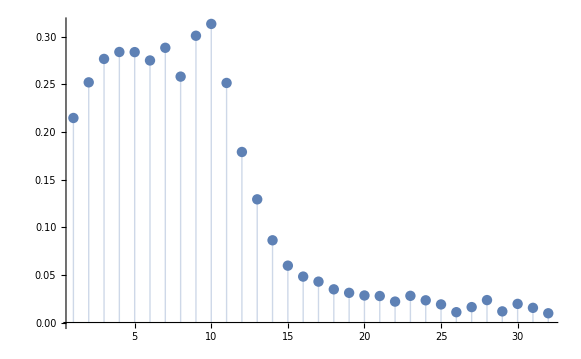

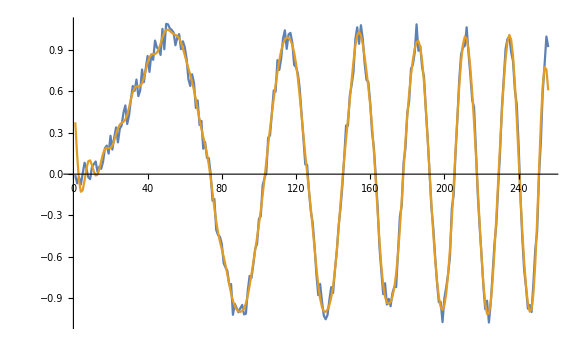

```mathematica
n=256;
k=32;
t=Pi;
func[x_]:=Sin[x^2]+RandomReal[{-0.1,0.1}]
f=Table[func[2*Pi*(i-1)/n],{i,1,n}];
sa0=Total[f]/n
sa=Table[Sum[f[[i]]*Cos[2*Pi*j*(i-1)/n],{i,1,n}]*2/n,{j,1,k}]//N;
sb=Table[Sum[f[[i]]*Sin[2*Pi*j*(i-1)/n],{i,1,n}]*2/n,{j,1,k}]//N;
sab=Table[Sqrt[sa[[j]]^2+sb[[j]]^2], {j, 1,k}];
ListPlot[sab,PlotRange->Full,Filling->Axis]
approx=Table[sa0+Sum[sa[[j]]*Cos[2*Pi*j*(i-1)/n]+sb[[j]]*Sin[2*Pi*j*(i-1)/n],{j,1,k}],{i, 1, n}];
ListLinePlot[{f,approx},PlotRange->Full]
```

```mathematica
Dwt[list_]:=(
If[Dimensions[list]=={1},Return[list]];
tmp=Table[(list[[j]]+list[[j+1]])/2,{j,1,Dimensions[list][[1]],2}]//N;

retval=Table[(list[[j]]-list[[j+1]])/2,{j,1,Dimensions[list][[1]],2}]//N;
dwt=Dwt[tmp];
AppendTo[retval,dwt];

Return[retval];
);
```

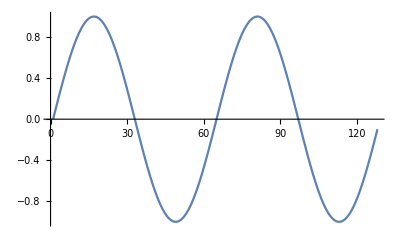

-Graphics-

{64}

```mathematica
n=128;
values=Table[Sin[(4*Pi)/n*x],{x, 0,n-1}];
ListLinePlot[values,PlotRange->Full]
While[
diff=Table[(values[[j]]-values[[j+1]])/2,{j,1,n-1,2}]//N;
sum=Table[(values[[j]]+values[[j+1]])/2,{j,1,n-1,2}]//N;
Image[{values*0.5+0.5},Magnification->8]
Dimensions[diff]
```

```mathematica
Trace[tmp=Table[(list[[j]]+list[[j+1]])/2,{j,1,Dimensions[list][[1]],2}]]
```

{{Table[1/2 (list⟦j⟧+list⟦j+1⟧),{j,1,Dimensions[list]⟦1⟧,2}],{}},tmp={},{}}